# Center of mass integral

## Coordinates & solutions

### Schwarzschild in isotropic Kerr-Schild coordinates

```mathematica
r[x_, y_, z_] :=√(x^2+y^2+z^2);
H[x_, y_, z_]:=M/r[x,y,z];
l[x_,y_,z_]:= {x/r[x,y,z],y/r[x,y,z],z/r[x,y,z]};
spatialMetric[x_,y_,z_]:=({{1+2 H[x,y,z] l[x,y,z][[1]] l[x,y,z][[1]], 2 H[x,y,z] l[x,y,z][[1]] l[x,y,z][[2]], 2 H[x,y,z] l[x,y,z][[1]] l[x,y,z][[3]]}, {2 H[x,y,z] l[x,y,z][[2]] l[x,y,z][[1]], 1+2 H[x,y,z] l[x,y,z][[2]] l[x,y,z][[2]], 2 H[x,y,z] l[x,y,z][[2]] l[x,y,z][[3]]}, {2 H[x,y,z] l[x,y,z][[3]] l[x,y,z][[1]], 2 H[x,y,z] l[x,y,z][[3]] l[x,y,z][[2]], 1+2 H[x,y,z] l[x,y,z][[3]] l[x,y,z][[3]]}});
lapse[x_,y_,z_]:=(√(1+(2 M)/r[x,y,z]))^-1;
```

```mathematica
admMassSurfaceIntegrand[x_,y_,z_]:= 1/(16 Pi) (lapse[x,y,z]^4 H[x,y,z])/r[x,y,z](4+8H[x,y,z])l[x,y,z];
paramSurface[R_,u_,v_]:={R Sin[u] Cos[v],R Sin[u] Sin[v],R Cos[u]};
admMass[R_]:=Integrate[Dot[admMassSurfaceIntegrand[x,y,z],l[x,y,z] r[x,y,z]^2 Sin[u]]
		/. {x->paramSurface[R,u,v][[1]],y->paramSurface[R,u,v][[2]],z->paramSurface[R,u,v][[3]]}, {u,0,Pi},{v,0,2 Pi}];
```

### Schwarzschild in isotropic coordinates

```mathematica
r[x_, y_, z_] := √(x^2+y^2+z^2);
conformalFactor[x_, y_, z_] := 1 + M/(2 r[x,y,z]);
spatialMetric[x_, y_, z_]:= ({{conformalFactor[x,y,z]^4, 0, 0}, {0, conformalFactor[x,y,z]^4, 0}, {0, 0, conformalFactor[x,y,z]^4}});
lapse[x_,y_,z_]:= (1 - M/(2 r[x,y,z]))/(1 + M/(2 r[x,y,z]));
admMass[R_]:= 1;
```

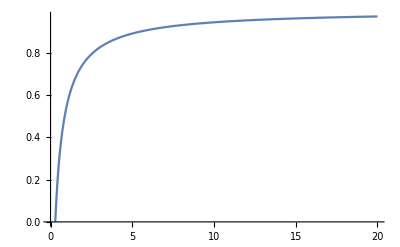

```mathematica
Plot[lapse[d,d,d] /. M->1, {d, 0, 20}, AxesOrigin->{0,0}]
```

## Relevant quantities

### Conformal decomposition

```mathematica
conformalFactor[x_,y_,z_]:=1;
```

```mathematica
conformalFactor[x_,y_,z_]:= Det[spatialMetric[x,y,z]]^-12;
```

### Outward-pointing unit normal

```mathematica
rVector[x_,y_,z_] := {x, y, z};
rMagnitude[x_,y_,z_] := Sum[Sum[
	spatialMetric[x,y,z][[i,j]] rVector[x,y,z][[i]] rVector[x,y,z][[j]]
, {j, 3}], {i, 3}];
unitNormal[x_,y_,z_] := rVector[x,y,z]/r[x,y,z];
```

## Center of mass integral

### Serguei’s version

```mathematica
centerOfMassSurfaceIntegrand[x_, y_, z_] := 
	3/(8 Pi)conformalFactor[x,y,z] unitNormal[x,y,z];
paramSurface[R_,u_,v_]:={R Sin[u] Cos[v],R Sin[u] Sin[v],R Cos[u]};
centerOfMass[R_] := 1/admMass[R] Integrate[
	centerOfMassSurfaceIntegrand[x,y,z] . r[x,y,z]^2 Sin[u]
/. {x->paramSurface[R,u,v][[1]],y->paramSurface[R,u,v][[2]],z->paramSurface[R,u,v][[3]]}
, {u,0,Pi},{v,0,2 Pi}];
```

```mathematica
centerOfMass[10000000] /. M-> 1 // N
```

NIntegrate::inumr: The integrand {(60000003 Cos[v] Sin[u])/(160000000 π),(60000003 Sin[u] Sin[v])/(160000000 π),(60000003 Cos[u])/(160000000 π)}.100000000000000 Sin[u] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[{(60000003 Cos[v] Sin[u])/(160000000 π),(60000003 Sin[u] Sin[v])/(160000000 π),(60000003 Cos[u])/(160000000 π)}.100000000000000 Sin[u],{u,0,π},{v,0,2 π}]